# Graviton Basis Toolkit Reference

This notebook is the notebook and PDF rendering of graviton_basis_toolkit_reference.md. It explains both the algorithms and how they are realized in graviton_basis_toolkit.wl.

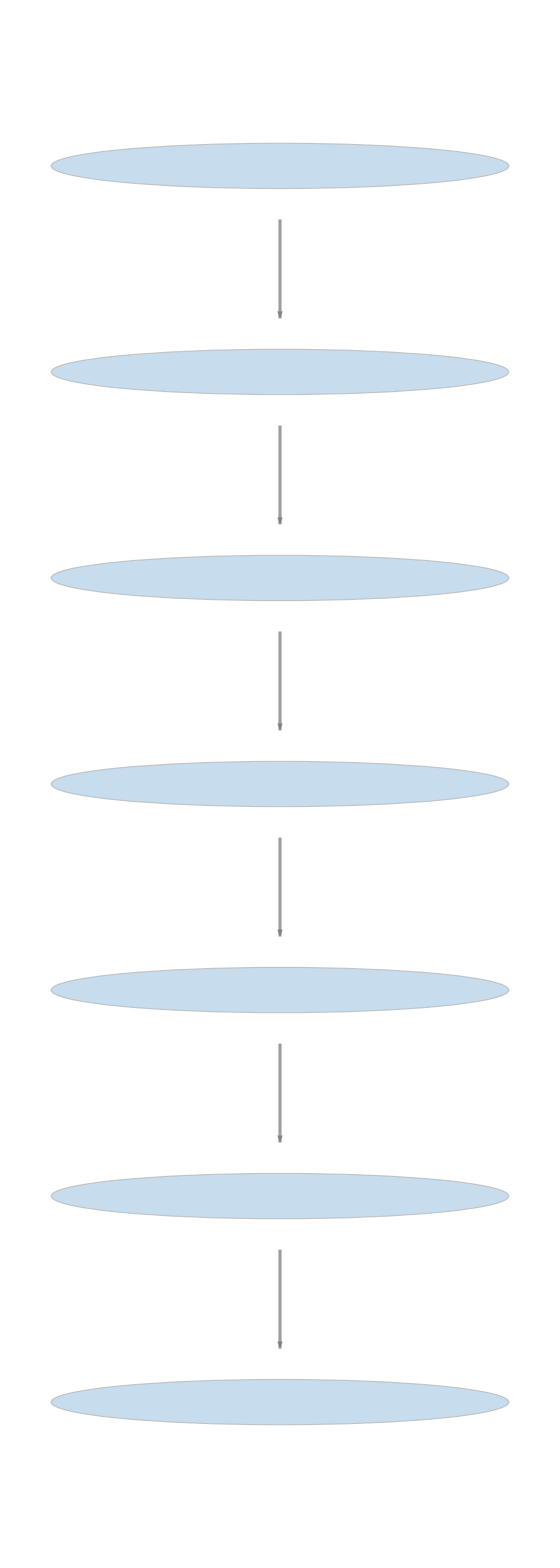

## Overall Architecture

The toolkit works sector by sector in the grading {nh, Nd}, where nh is the number of graviton fields and Nd is the number of derivatives. For each sector it constructs a raw scalar basis, quotients by total derivatives using the Euler operator, and then removes the image of Fierz-Pauli field redefinitions in the interaction sectors.

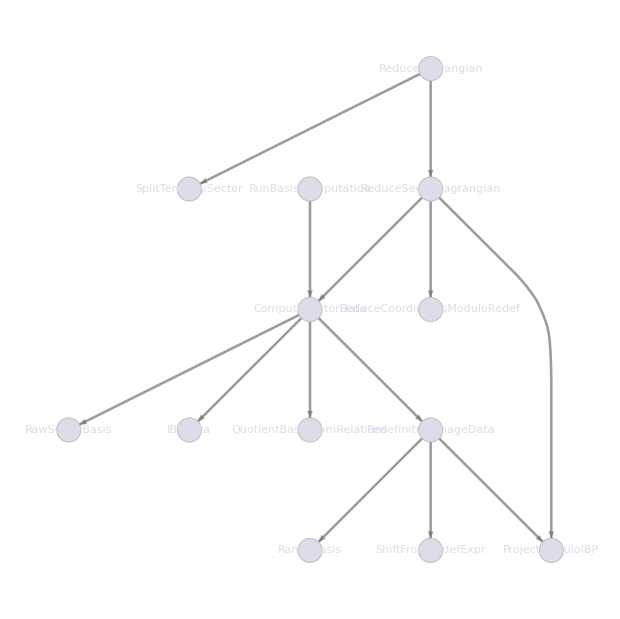

## Code Organization

Public API and options

xAct setup for M, eta, PD, h, dh, probe, and lam

Utilities, canonicalization, sector keys, and cache helpers

Raw scalar-basis generation from ordered derivative partitions

IBP relations via VarD and SolveConstants

Field-redefinition image via the Fierz-Pauli variation

Sector assembly, summaries, and the Lagrangian reducer API

## Canonicalization

canonExpr is the core normal-form map. It expands the expression, contracts metrics, canonicalizes tensor symmetries, sorts nested PD operators, canonicalizes again, and finally collects tensor structures. The second canonicalization pass after SortCovDs is essential for eliminating fake distinctions caused by reordered commuting scalar derivatives.

## Raw Basis Generation

RawScalarBasis[nh, Nd] builds all ordered ways of distributing Nd derivatives across nh graviton fields, forms the corresponding monomials, applies AllContractions, and canonicalizes the results. Ordered partitions are necessary because different derivative placements become equivalent only after canonicalization, not before.

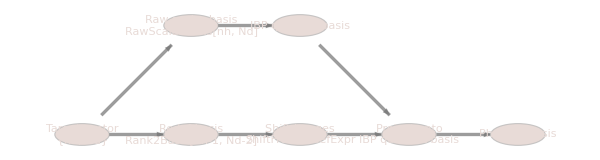

## IBP Quotient

IBPData constructs a generic linear combination of the raw basis and applies the Euler-Lagrange operator VarD[h[-m,-n], PD]. A scalar density is a total derivative exactly when its Euler derivative vanishes, so solving VarD[ansatz] == 0 gives the full space of IBP relations. QuotientBasisFromRelations then removes pivot columns to produce an IBP basis.

## Field-Redefinition Quotient

For a target sector {nh, Nd}, the relevant redefinitions have rank-2 basis Rank2Basis[nh-1, Nd-2]. ShiftFromRedefExpr computes the linearized variation of the Fierz-Pauli Lagrangian under h -> h + lam dh and substitutes a concrete delta h. Each resulting image is projected onto the IBP basis, the independent image vectors are extracted, and their span is removed from the IBP quotient basis.

Quadratic sectors are intentionally not quotiented by field redefinitions. At nh < 3, linear redefinitions act directly on the kinetic operator itself, so removing those directions is not the right equivalence relation for classifying the quadratic action.

## Reducer API

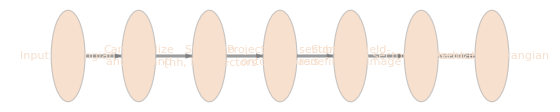

ReduceSectorLagrangian takes an expression and an explicit sector label, projects the expression into the IBP basis, subtracts the field-redefinition image component, and returns the remaining physical representative together with all intermediate coordinates.

ReduceLagrangian canonicalizes and expands the input, splits it term by term into sectors, applies ReduceSectorLagrangian to each sector, and then sums the reduced representatives.

## Main Public Functions

RunBasisComputation

ComputeSectorData

RawBasisOfSector, IBPBasisOfSector, PhysicalBasisOfSector

RedefinitionRulesOfSector

ReduceSectorLagrangian, ReduceLagrangian

## Implementation Notes

Odd-derivative scalar sectors are empty in this setup and are skipped early.

The cache is per intermediate object, not only per final sector summary.

ProjectModuloIBP sets any remaining unsolved ansatz coefficients to zero so returned coordinates are concrete.

The current automatic splitter assumes the input uses the same h, eta, and PD conventions as the toolkit itself.